# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["/Users/pcs/Desktop/Entropy/Calculations/QMB_offline.wl"];
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

```mathematica
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

# Schmidt coefficients

## g

```mathematica
L=10;
```

```mathematica
J=1;
h=1.;
g=1;
H=IsingNNOpenHamiltonian[h,g,J,L];
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,1,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
```

```mathematica
La=L/2;
Lb=L-La;
eigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,newall[[All,2]]},DistributedContexts->Full];
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
```

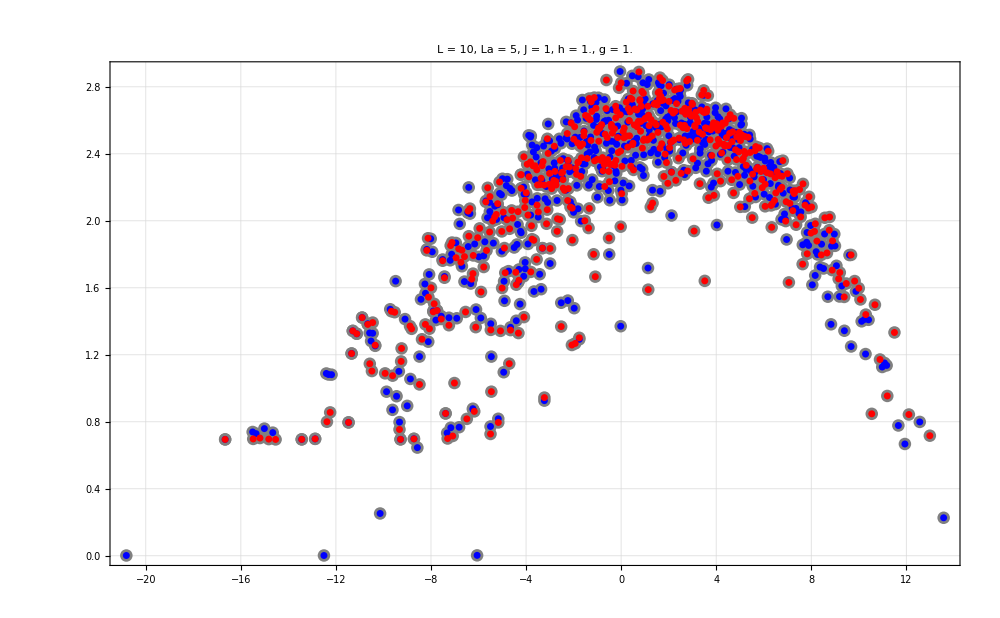

```mathematica
ListPlot[{Transpose[{newall[[All,1]],eigenvecdiag}],Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Gray,PointSize[0.009]],Directive[Blue,PointSize[0.005]],Directive[Red,PointSize[0.005]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black]]
```

```mathematica
differences=Table[Abs[i-j],{i,eveneigenval},{j,eveneigenval}];
```

```mathematica
MatrixPlot[differences,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
tol=10^-10;
diffs=Flatten@Outer[Subtract,eveneigenval,eveneigenval];
approxZeroDiffs=Select[DeleteCases[diffs,0],Abs[#]<tol&]
eveneigenval//Length
approxZeroDiffs//Length
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

528

528

```mathematica
differences=Table[Abs[i-j],{i,oddeigenval},{j,oddeigenval}];
```

```mathematica
MatrixPlot[differences,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
tol=10^-10;
diffs=Flatten@Outer[Subtract,oddeigenval,oddeigenval];
approxZeroDiffs=Select[DeleteCases[diffs,0],Abs[#]<tol&]
oddeigenval//Length
approxZeroDiffs//Length
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

496

496

## Full dimension

```mathematica
productstate2=Table[RandomChainProductState[L],500];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,productstate2},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,productstate2}],First];
productstate=data[[1,2]];
```

```mathematica
rhoeigen=Dyad[Conjugate[allvecs].productstate];
rhoaeigen=MatrixPartialTrace[rhoeigen,2,{2^(L/2),2^(L/2)}];
```

```mathematica
schmidteigen=Chop[Eigenvalues[rhoaeigen]]
sdiagonal=-Total[schmidteigen*Log[schmidteigen]]
```

{0.110325,0.101499,0.0883033,0.0801756,0.0704973,0.0619589,0.0588281,0.0523741,0.0476486,0.041125,0.0396433,0.0329541,0.0313944,0.0295345,0.0266521,0.0217018,0.0180695,0.0156887,0.0148706,0.0120164,0.0104459,0.00880932,0.0075045,0.00628968,0.0037181,0.00332396,0.00224811,0.00121484,0.000728313,0.000308921,0.0000980484,0.0000501449}

2.96372

```mathematica
La=L/2;
Lb=L-La;
tlist=Table[10^i,{i,-2,10,0.0025}];
tlist//Length
```

4801

```mathematica
svntproduct=ParallelTable[{t,svn[L,La,Lb,productstate,allvals,allvecs,t]},{t,tlist},DistributedContexts->Full];
```

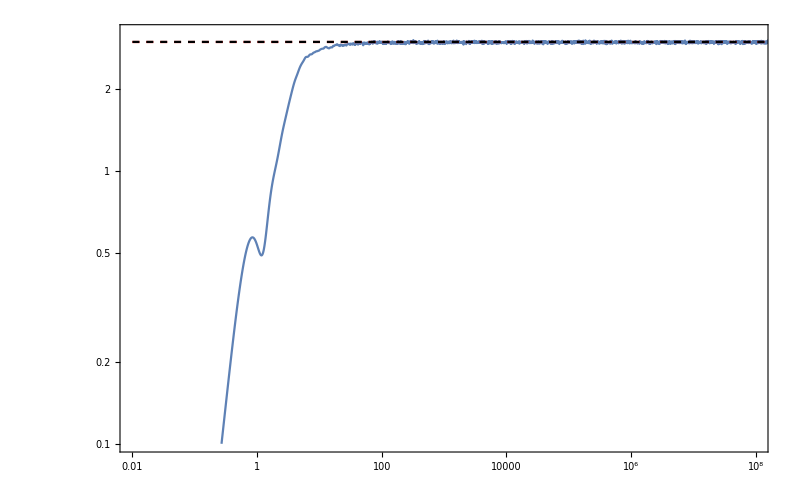

```mathematica
plot3=Show[{ListLogLogPlot[svntproduct,PlotRange->{{10^-2,10^8},{0.1,3.2}},Joined->True,ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{sdiagonal,pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]}]
```

## By parity

## Positive

```mathematica
Peven=(1/2)(IdentityMatrix[2^L]+R);
evenproductstate=Normalize[Peven.productstate];
rhoeigen=Dyad[Conjugate[allvecs].evenproductstate];
rhoaeigen=MatrixPartialTrace[rhoeigen,2,{2^(L/2),2^(L/2)}];
schmidteigen=Chop[Eigenvalues[rhoaeigen]]
sdiagonal=-Total[schmidteigen*Log[schmidteigen]]
```

{0.154144,0.135443,0.120736,0.0987903,0.0915182,0.0788116,0.0698902,0.0484859,0.0393233,0.0377394,0.0310336,0.0263065,0.0235599,0.0168491,0.0128926,0.00896697,0.00550936,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Indeterminate

```mathematica
schmidteigen=Chop[Eigenvalues[rhoaeigen]][[1;;-16]]
sdiagonal=-Total[schmidteigen*Log[schmidteigen]]
```

{0.154144,0.135443,0.120736,0.0987903,0.0915182,0.0788116,0.0698902,0.0484859,0.0393233,0.0377394,0.0310336,0.0263065,0.0235599,0.0168491,0.0128926,0.00896697,0.00550936}

2.53325

```mathematica
svntproduct=ParallelTable[{t,svn[L,La,Lb,evenproductstate,allvals,allvecs,t]},{t,tlist},DistributedContexts->Full];
```

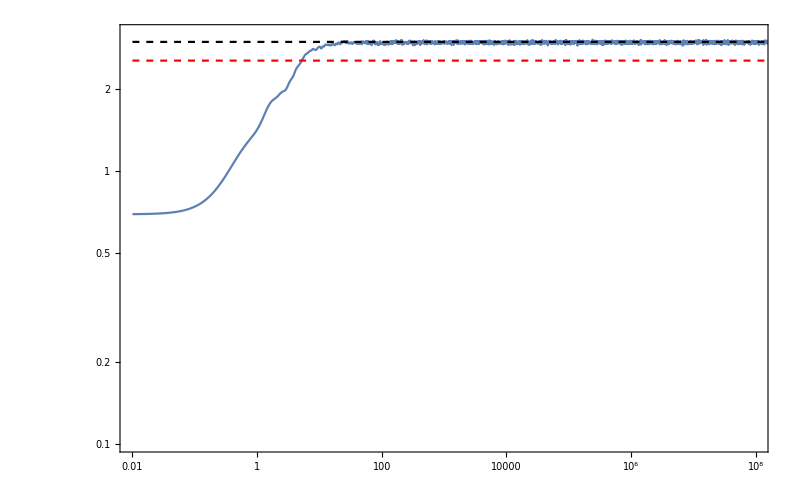

```mathematica
plot1=Show[{ListLogLogPlot[svntproduct,PlotRange->{{10^-2,10^8},{0.1,3.2}},Joined->True,ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{sdiagonal,pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]}]
```

## Negative

```mathematica
Podd=(1/2)(IdentityMatrix[2^L]-R);
```

```mathematica
evenproductstate=Normalize[Podd.productstate];
rhoeigen=Dyad[Conjugate[allvecs].evenproductstate];
rhoaeigen=MatrixPartialTrace[rhoeigen,2,{2^(L/2),2^(L/2)}];
schmidteigen=Chop[Eigenvalues[rhoaeigen]]
sdiagonal=-Total[schmidteigen*Log[schmidteigen]]
```

{0.149251,0.132318,0.116582,0.0974793,0.085651,0.079255,0.0657872,0.0566411,0.0541377,0.0404971,0.0380153,0.0264428,0.0225395,0.0168485,0.0111731,0.00738242,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Indeterminate

```mathematica
schmidteigen=Chop[Eigenvalues[rhoaeigen]][[1;;-9]]
sdiagonal=-Total[schmidteigen*Log[schmidteigen]]
```

{0.149251,0.132318,0.116582,0.0974793,0.085651,0.079255,0.0657872,0.0566411,0.0541377,0.0404971,0.0380153,0.0264428,0.0225395,0.0168485,0.0111731,0.00738242,0,0,0,0,0,0,0,0}

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Indeterminate

```mathematica
svntproduct=ParallelTable[{t,svn[L,La,Lb,evenproductstate,allvals,allvecs,t]},{t,tlist},DistributedContexts->Full];
```

```mathematica
plot2=Show[{ListLogLogPlot[svntproduct,PlotRange->{{10^-2,10^8},{0.1,3.2}},Joined->True,ImageSize->800,PlotStyle->Directive[Purple,Dotted]],LogLogPlot[{sdiagonal,pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]}];
```

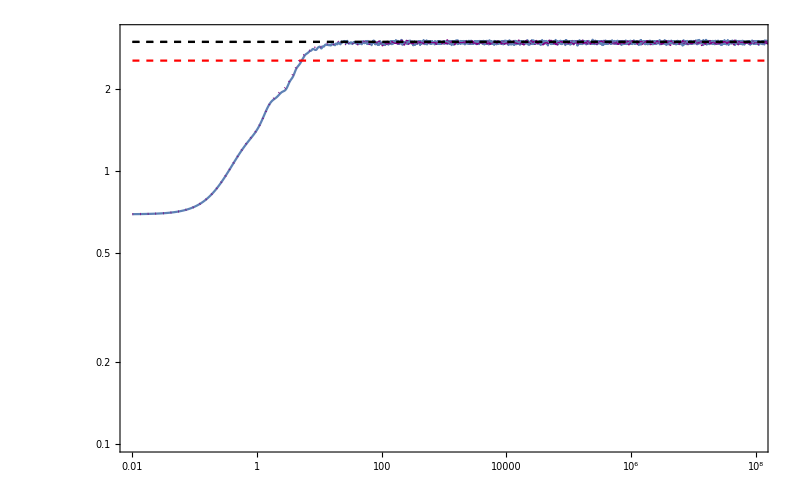

```mathematica
Show[{plot1,plot2}]
```

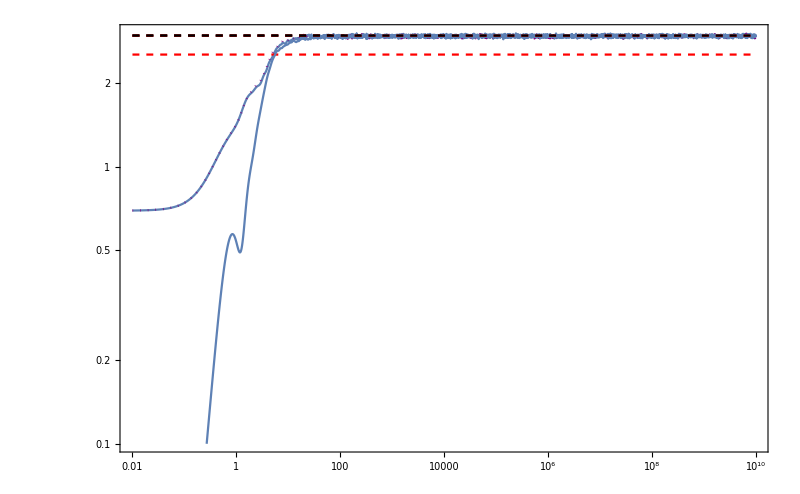

```mathematica
Show[{plot1,plot2,plot3},PlotRange->All]
```

## Product state in positive sector

```mathematica
allstates={};
Do[
state=RandomQubitState[];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@Table[state,L/2]],Flatten[KroneckerProduct@@Table[state,L/2]]]];
AppendTo[allstates,evenini];
,{i,500}];
```

```mathematica
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,allstates}],First];
productstate=data[[1,2]];
```

```mathematica
Chop[Conjugate[productstate].Peven.productstate]
```

1.

```mathematica
svntproduct=ParallelTable[{t,svn[L,La,Lb,productstate,allvals,allvecs,t]},{t,tlist},DistributedContexts->Full];
```

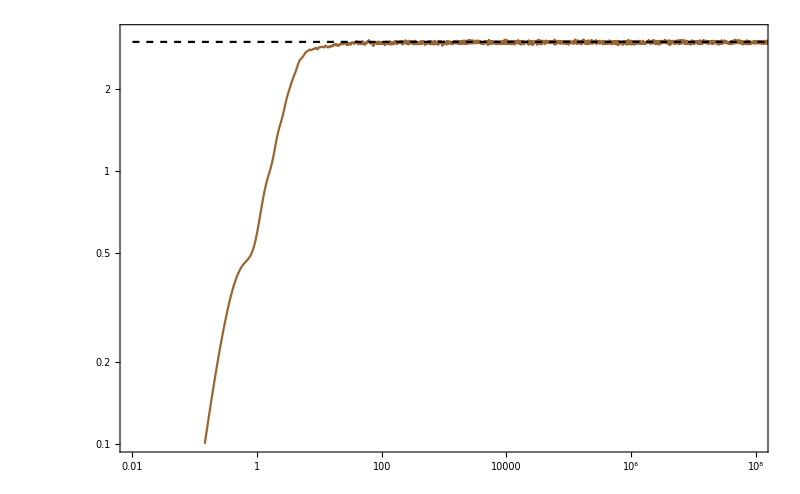

```mathematica
plot4=Show[{ListLogLogPlot[svntproduct,PlotRange->{{10^-2,10^8},{0.1,3.2}},Joined->True,PlotStyle->Directive[Brown],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{sdiagonal,pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]}]
```

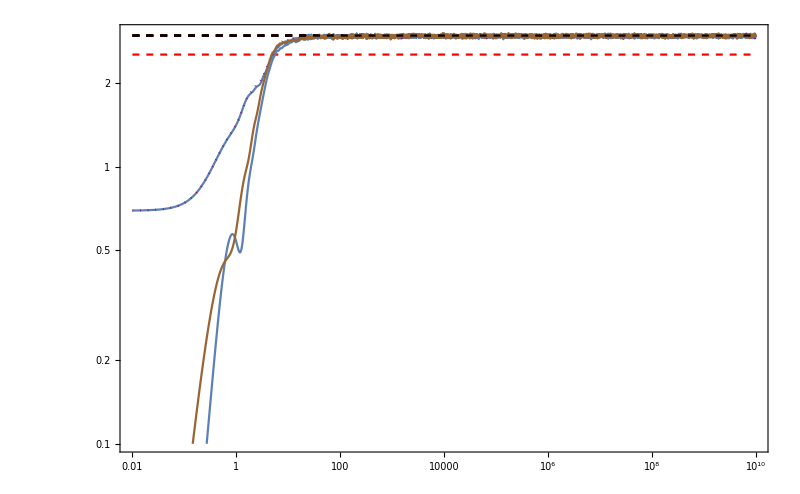

```mathematica
Show[{plot1,plot2,plot3,plot4},PlotRange->All]
```